# Slater-type orbitals in PPSTM d-orb decay

This was calculations of STO decay for d-orbitals for https://github.com/ondrejkrejci/PPSTM/tree/dOrbSlaterDecay

```mathematica
(*eV=0.036749034;(*eV to Hertree (atomic units)*)
aB=1.889725989;(*Angstrom to Bohr radius*)*)
nstar={1,2,3,3.7,4.0,4.2,4.3};
dzeta1={};dzeta2={};s01={};s02={};nstar01={};nstar02={};Nnorm1={};Nnorm2={};
For[n=1,n≤118,n++,{
conf=ElementData[n,"ElectronConfiguration"],
ntmp=Length[conf],
s=0,
tmpconf=Table[0*i*j,{i,ntmp},{j,4}],
For[i=1,i≤ntmp,i++,For[j=1,j≤Length[conf[[i]] ],j++,tmpconf[[i,j]]=conf[[i,j]]]],
scrennN[i_]:=If[i==ntmp,0.35*(tmpconf[[i,1]]+tmpconf[[i,2]]-1),
If[i==ntmp-1,0.85*(tmpconf[[i,1]]+tmpconf[[i,2]]+tmpconf[[i,3]]+tmpconf[[i,4]]),
(tmpconf[[i,1]]+tmpconf[[i,2]]+tmpconf[[i,3]]+tmpconf[[i,4]])] ],
If[n==1,s1=0,If[n==2,s1=0.30,s1=Sum[scrennN[i],{i,ntmp}]]],
s01=Append[s01,s1 ],
nstar01=Append[nstar01,nstar[[ntmp]] ],
dzeta1=Append[dzeta1,(n-s1)/nstar[[ntmp]] ],
Nnorm1=Append[Nnorm1,(2*dzeta1[[n]])^(ntmp+0.5)/Sqrt[Factorial[2ntmp]]],
If[n<11,{s2=None,dzetatmp2=0,nstartmp=None,norm2tmp=None},{
scrennD[i_]:=If[i==ntmp-1,0.35*(tmpconf[[i,3]]-1)+1*(tmpconf[[i,1]]+tmpconf[[i,2]]),
(tmpconf[[i,1]]+tmpconf[[i,2]]+tmpconf[[i,3]]+tmpconf[[i,4]])] ,
s2=Sum[scrennD[i],{i,ntmp-1}],
nstartmp=nstar[[ntmp-1]],
dzetatmp2=(n-s2)/nstartmp,
norm2tmp=(2*dzetatmp2)^(ntmp-0.5)/Sqrt[Factorial[2(ntmp-1)]],
}],
s02=Append[s02,s2 ],
nstar02=Append[nstar02,nstartmp ],
dzeta2=Append[dzeta2,dzetatmp2 ],
Nnorm2=Append[Nnorm2,norm2tmp]
}]
s01
nstar01
dzeta1
Nnorm1

s02
nstar02
dzeta2
Nnorm2
```

{0,0.3,1.7,2.05,2.4,2.75,3.1,3.45,3.8,4.15,8.8,9.15,9.5,9.85,10.2,10.55,10.9,11.25,16.8,17.15,18.,18.85,19.7,21.05,21.4,22.25,23.1,23.95,25.3,25.65,26.,26.35,26.7,27.05,27.4,27.75,34.8,35.15,36.,36.85,38.2,39.05,39.4,40.75,41.6,27.75,43.3,43.65,44.,44.35,44.7,45.05,45.4,45.75,52.8,53.15,54.,55.,56.15,57.15,58.15,59.15,60.15,61.,62.15,63.15,64.15,65.15,66.15,67.15,68.,68.85,69.7,70.55,71.4,72.25,73.1,74.45,75.3,75.65,76.,76.35,76.7,77.05,77.4,77.75,84.8,85.15,86.,86.85,88.,89.,90.,91.15,92.15,93.,94.15,95.15,96.15,97.15,98.15,99.15,99.5,100.85,101.7,102.55,103.4,104.25,105.1,106.45,107.3,107.65,108.,108.35,108.7,109.05,109.4,109.75}

{1,1,2,2,2,2,2,2,2,2,3,3,3,3,3,3,3,3,3.7,3.7,3.7,3.7,3.7,3.7,3.7,3.7,3.7,3.7,3.7,3.7,3.7,3.7,3.7,3.7,3.7,3.7,4.,4.,4.,4.,4.,4.,4.,4.,4.,3.7,4.,4.,4.,4.,4.,4.,4.,4.,4.2,4.2,4.2,4.2,4.2,4.2,4.2,4.2,4.2,4.2,4.2,4.2,4.2,4.2,4.2,4.2,4.2,4.2,4.2,4.2,4.2,4.2,4.2,4.2,4.2,4.2,4.2,4.2,4.2,4.2,4.2,4.2,4.3,4.3,4.3,4.3,4.3,4.3,4.3,4.3,4.3,4.3,4.3,4.3,4.3,4.3,4.3,4.3,4.3,4.3,4.3,4.3,4.3,4.3,4.3,4.3,4.3,4.3,4.3,4.3,4.3,4.3,4.3,4.3}

{1,1.7,0.65,0.975,1.3,1.625,1.95,2.275,2.6,2.925,0.733333,0.95,1.16667,1.38333,1.6,1.81667,2.03333,2.25,0.594595,0.77027,0.810811,0.851351,0.891892,0.797297,0.972973,1.01351,1.05405,1.09459,1.,1.17568,1.35135,1.52703,1.7027,1.87838,2.05405,2.22973,0.55,0.7125,0.75,0.7875,0.7,0.7375,0.9,0.8125,0.85,4.93243,0.925,1.0875,1.25,1.4125,1.575,1.7375,1.9,2.0625,0.52381,0.678571,0.714286,0.714286,0.678571,0.678571,0.678571,0.678571,0.678571,0.714286,0.678571,0.678571,0.678571,0.678571,0.678571,0.678571,0.714286,0.75,0.785714,0.821429,0.857143,0.892857,0.928571,0.845238,0.880952,1.03571,1.19048,1.34524,1.5,1.65476,1.80952,1.96429,0.511628,0.662791,0.697674,0.732558,0.697674,0.697674,0.697674,0.662791,0.662791,0.697674,0.662791,0.662791,0.662791,0.662791,0.662791,0.662791,0.813953,0.732558,0.767442,0.802326,0.837209,0.872093,0.906977,0.825581,0.860465,1.01163,1.16279,1.31395,1.46512,1.61628,1.76744,1.9186}

{2.,4.43306,0.393326,1.08388,2.22499,3.88689,6.13135,9.01411,12.5864,16.896,0.142395,0.352348,0.72319,1.31275,2.18453,3.40724,5.05439,7.20406,0.010861,0.0348152,0.0438543,0.0546216,0.067341,0.0406599,0.0996158,0.119704,0.14281,0.169245,0.112687,0.233436,0.43685,0.757155,1.23595,1.92264,2.87494,4.1592,0.000886703,0.00368214,0.00488225,0.00638501,0.00334059,0.00445117,0.0133081,0.00758249,0.00971824,148.132,0.0154726,0.0376829,0.0810566,0.158752,0.288953,0.495872,0.810827,1.27336,0.0000618235,0.000332581,0.000464188,0.000464188,0.000332581,0.000332581,0.000332581,0.000332581,0.000332581,0.000464188,0.000332581,0.000332581,0.000332581,0.000332581,0.000332581,0.000332581,0.000464188,0.000637419,0.000862475,0.00115141,0.00151835,0.00197975,0.00255462,0.00138641,0.00181433,0.00519501,0.0128443,0.0284263,0.0576925,0.109221,0.195296,0.332933,4.02418×10^-6,0.0000280442,0.0000412019,0.0000594069,0.0000412019,0.0000412019,0.0000412019,0.0000280442,0.0000280442,0.0000412019,0.0000280442,0.0000280442,0.0000280442,0.0000280442,0.0000280442,0.0000280442,0.000130924,0.0000594069,0.0000842097,0.000117531,0.000161725,0.000219655,0.000294776,0.00014562,0.000198619,0.000668616,0.00190013,0.00475194,0.0107538,0.0224592,0.0439146,0.0812666}

{None,None,None,None,None,None,None,None,None,None,9.65,9.65,9.65,9.65,9.65,9.65,9.65,9.65,17.65,17.65,18.,18.35,18.7,19.4,19.4,19.75,20.1,20.45,21.15,21.15,21.15,21.15,21.15,21.15,21.15,21.15,35.65,35.65,36.,36.35,37.05,37.4,37.4,38.1,38.45,21.15,39.15,39.15,39.15,39.15,39.15,39.15,39.15,39.15,53.65,53.65,54.,55.,56.65,57.65,58.65,59.65,60.65,61.,62.65,63.65,64.65,65.65,66.65,67.65,68.,68.35,68.7,69.05,69.4,69.75,70.1,70.8,71.15,71.15,71.15,71.15,71.15,71.15,71.15,71.15,85.65,85.65,86.,86.35,88.,89.,90.,91.65,92.65,93.,94.65,95.65,96.65,97.65,98.65,99.65,99.65,100.35,100.7,101.05,101.4,101.75,102.1,102.8,103.15,103.15,103.15,103.15,103.15,103.15,103.15,103.15}

{None,None,None,None,None,None,None,None,None,None,2,2,2,2,2,2,2,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3.7,3.7,3.7,3.7,3.7,3.7,3.7,3.7,3.7,3,3.7,3.7,3.7,3.7,3.7,3.7,3.7,3.7,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.,4.2,4.2,4.2,4.2,4.2,4.2,4.2,4.2,4.2,4.2,4.2,4.2,4.2,4.2,4.2,4.2,4.2,4.2,4.2,4.2,4.2,4.2,4.2,4.2,4.2,4.2,4.2,4.2,4.2,4.2,4.2,4.2}

{0,0,0,0,0,0,0,0,0,0,0.675,1.175,1.675,2.175,2.675,3.175,3.675,4.175,0.45,0.783333,1.,1.21667,1.43333,1.53333,1.86667,2.08333,2.3,2.51667,2.61667,2.95,3.28333,3.61667,3.95,4.28333,4.61667,4.95,0.364865,0.635135,0.810811,0.986486,1.06757,1.24324,1.51351,1.59459,1.77027,8.28333,2.12162,2.39189,2.66216,2.93243,3.2027,3.47297,3.74324,4.01351,0.3375,0.5875,0.75,0.75,0.5875,0.5875,0.5875,0.5875,0.5875,0.75,0.5875,0.5875,0.5875,0.5875,0.5875,0.5875,0.75,0.9125,1.075,1.2375,1.4,1.5625,1.725,1.8,1.9625,2.2125,2.4625,2.7125,2.9625,3.2125,3.4625,3.7125,0.321429,0.559524,0.714286,0.869048,0.714286,0.714286,0.714286,0.559524,0.559524,0.714286,0.559524,0.559524,0.559524,0.559524,0.559524,0.559524,0.797619,0.869048,1.02381,1.17857,1.33333,1.4881,1.64286,1.71429,1.86905,2.10714,2.34524,2.58333,2.82143,3.05952,3.29762,3.53571}

{None,None,None,None,None,None,None,None,None,None,0.432244,1.72808,4.19282,8.05596,13.5138,20.741,29.896,41.1254,0.025774,0.179371,0.421637,0.837605,1.48646,1.8822,3.7469,5.50294,7.78012,10.6618,12.2196,18.5916,27.0421,37.9331,51.645,68.5765,89.1433,113.778,0.00120634,0.0146141,0.0438543,0.105995,0.151236,0.300177,0.727467,0.920028,1.47249,689.694,3.32568,5.70442,9.23485,14.2692,21.2178,30.5514,42.8046,58.5782,0.0000604351,0.00127446,0.00488225,0.00488225,0.00127446,0.00127446,0.00127446,0.00127446,0.00127446,0.00488225,0.00127446,0.00127446,0.00127446,0.00127446,0.00127446,0.00127446,0.00488225,0.014357,0.0353614,0.0766977,0.151178,0.276563,0.476566,0.602258,0.968806,1.87345,3.37561,5.74536,9.33049,14.5687,22.0002,32.2812,2.58568×10^-6,0.0000949177,0.000464188,0.00166077,0.000464188,0.000464188,0.000464188,0.0000949177,0.0000949177,0.000464188,0.0000949177,0.0000949177,0.0000949177,0.0000949177,0.0000949177,0.0000949177,0.000951037,0.00166077,0.00481893,0.0120321,0.0268305,0.0547805,0.104214,0.137426,0.241023,0.525457,1.05376,1.9756,3.50409,5.93303,9.65672,15.1925}

```mathematica
i=26;j=4;
Integrate[Nnorm1[[i]]^2*r^(2*j)*Exp[-2*dzeta1[[i]]*r],{r,0,Infinity}]
i=26;j=3;
Integrate[Nnorm2[[i]]^2*r^(2*j)*Exp[-2*dzeta2[[i]]*r],{r,0,Infinity}]
```

1.

1.

```mathematica
F[r_,i_,j_]:=If[j==1,Nnorm1[[i]]*r^(ElementData[26,"Period"]-1)*Exp[-dzeta1[[i]]*r],Nnorm2[[i]]*r^(ElementData[26,"Period"]-2)*Exp[-dzeta2[[i]]*r]]
aB=1.889725989;(*Angstrom to Bohr radius*)
```

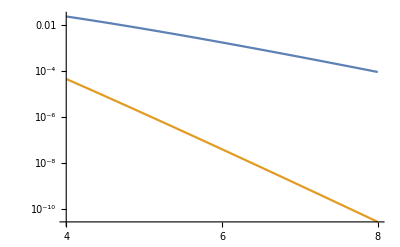

```mathematica
LogPlot[{F[r,26,1],F[r,26,2]},{r,4*aB,8*aB},Ticks->{Table[{i*aB,i},{i,0,8}],Automatic}]
```

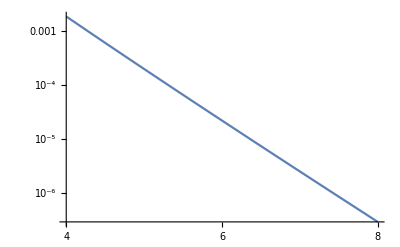

```mathematica
LogPlot[{F[r,26,2]/F[r,26,1]},{r,4*aB,8*aB},Ticks->{Table[{i*aB,i},{i,0,8}],Automatic}]
```

```mathematica
4aB
8aB
11/aB
```

7.5589

15.1178

5.82095

```mathematica
i=26
data=Table[{r,F[r,i,2]/F[r,i,1]},{r,7.6,15.1,0.1}];
G[r_]:=A*Exp[-B*r]
fit=FindFit[data,A*Exp[-B*r],{A,B},r]
```

26

{A→14.9879,B→1.18947}

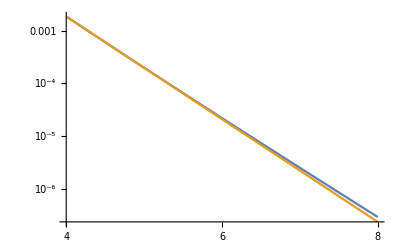

```mathematica
LogPlot[{F[r,26,2]/F[r,26,1],G[r]/.fit},{r,4*aB,8*aB},Ticks->{Table[{i*aB,i},{i,0,8}],Automatic}]
```

```mathematica
out0={};
For[n=1,n≤118,n++,{
If[n<11,out0=Append[out0,{n,A-> 0.,B-> 0.}],
{data=Table[{r,F[r,n,2]/F[r,n,1]},{r,7.6,15.1,0.1}],
fit=FindFit[data,A*Exp[-B*r],{A,B},r],
out0=Append[out0,Prepend[fit,n]]}
]
}]
out0
```

{{1,A→0.,B→0.},{2,A→0.,B→0.},{3,A→0.,B→0.},{4,A→0.,B→0.},{5,A→0.,B→0.},{6,A→0.,B→0.},{7,A→0.,B→0.},{8,A→0.,B→0.},{9,A→0.,B→0.},{10,A→0.,B→0.},{11,A→0.767918,B→0.0328932},{12,A→1.37102,B→0.326359},{13,A→1.75701,B→0.619026},{14,A→1.94855,B→0.908029},{15,A→2.01763,B→1.1947},{16,A→2.01982,B→1.4802},{17,A→1.98621,B→1.76505},{18,A→1.93391,B→2.04951},{19,A→0.581661,B→-0.0561258},{20,A→1.33702,B→0.106675},{21,A→2.65487,B→0.289199},{22,A→4.48152,B→0.471724},{23,A→6.73661,B→0.652975},{24,A→14.5944,B→0.851523},{25,A→12.078,B→1.01145},{26,A→14.9879,B→1.18947},{27,A→17.9679,B→1.36705},{28,A→20.9664,B→1.54433},{29,A→36.3806,B→1.73994},{30,A→26.8629,B→1.89828},{31,A→20.9746,B→2.05652},{32,A→17.0423,B→2.21468},{33,A→14.2631,B→2.37278},{34,A→12.2115,B→2.53083},{35,A→10.6442,B→2.68883},{36,A→9.41316,B→2.8468},{37,A→0.328392,B→-0.0979355},{38,A→0.997163,B→0.013244},{39,A→2.37082,B→0.156088},{40,A→4.5995,B→0.299366},{41,A→13.2393,B→0.474052},{42,A→20.4256,B→0.616368},{43,A→16.9117,B→0.726696},{44,A→38.482,B→0.898313},{45,A→48.7801,B→1.03835},{46,A→1.614,B→3.47839},{47,A→70.6818,B→1.31735},{48,A→50.0893,B→1.42591},{49,A→37.9011,B→1.53436},{50,A→30.0425,B→1.64273},{51,A→24.6453,B→1.75103},{52,A→20.7553,B→1.85927},{53,A→17.8431,B→1.96746},{54,A→15.5952,B→2.07562},{55,A→0.235853,B→-0.0991465},{56,A→0.957988,B→-0.000903731},{57,A→2.75151,B→0.130109},{58,A→2.75151,B→0.130109},{59,A→0.957988,B→-0.000903731},{60,A→0.957988,B→-0.000903731},{61,A→0.957988,B→-0.000903731},{62,A→0.957988,B→-0.000903731},{63,A→0.957988,B→-0.000903731},{64,A→2.75151,B→0.130109},{65,A→0.957988,B→-0.000903731},{66,A→0.957988,B→-0.000903731},{67,A→0.957988,B→-0.000903731},{68,A→0.957988,B→-0.000903731},{69,A→0.957988,B→-0.000903731},{70,A→0.957988,B→-0.000903731},{71,A→2.75151,B→0.130109},{72,A→6.16202,B→0.261506},{73,A→11.7075,B→0.393029},{74,A→19.7421,B→0.52412},{75,A→30.3954,B→0.654426},{76,A→43.6208,B→0.783951},{77,A→59.2683,B→0.912862},{78,A→140.299,B→1.07324},{79,A→174.24,B→1.20131},{80,A→118.442,B→1.29736},{81,A→86.8067,B→1.39332},{82,A→67.0924,B→1.48918},{83,A→53.9241,B→1.58498},{84,A→44.6506,B→1.68073},{85,A→37.8432,B→1.77642},{86,A→32.6768,B→1.87206},{87,A→0.154795,B→-0.103157},{88,A→0.842364,B→-0.0134893},{89,A→2.92738,B→0.110345},{90,A→7.57868,B→0.234523},{91,A→2.92738,B→0.110345},{92,A→2.92738,B→0.110345},{93,A→2.92738,B→0.110345},{94,A→0.842364,B→-0.0134893},{95,A→0.842364,B→-0.0134893},{96,A→2.92738,B→0.110345},{97,A→0.842364,B→-0.0134893},{98,A→0.842364,B→-0.0134893},{99,A→0.842364,B→-0.0134893},{100,A→0.842364,B→-0.0134893},{101,A→0.842364,B→-0.0134893},{102,A→0.842364,B→-0.0134893},{103,A→1.86548,B→0.0762809},{104,A→7.57868,B→0.234523},{105,A→16.1663,B→0.3589},{106,A→30.0122,B→0.483018},{107,A→50.1411,B→0.606492},{108,A→77.1908,B→0.729237},{109,A→111.458,B→0.851364},{110,A→302.887,B→1.00639},{111,A→393.741,B→1.12763},{112,A→256.702,B→1.2154},{113,A→182.207,B→1.30307},{114,A→137.302,B→1.39065},{115,A→108.107,B→1.47817},{116,A→88.0057,B→1.56562},{117,A→73.5287,B→1.65302},{118,A→62.7205,B→1.74038}}

```mathematica
Export["~/Desktop/tmp.dat",out0,"Table"]
```

~/Desktop/tmp.dat

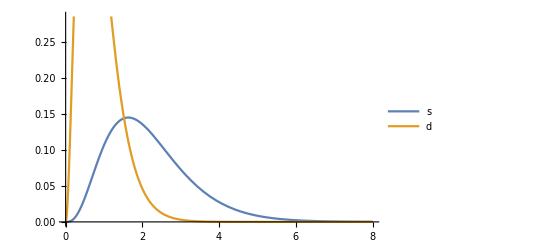

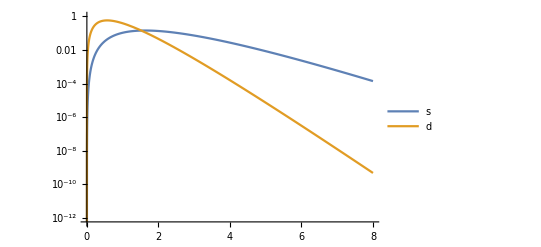

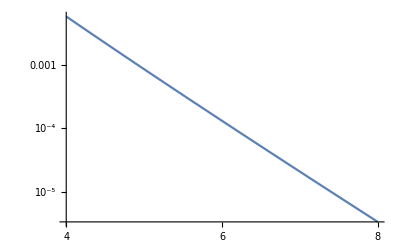

```mathematica
n=25;
Plot[{F[r,n,1],F[r,n,2]},{r,0*aB,8*aB},Ticks->{Table[{i*aB,i},{i,0,8}],Automatic},PlotLegends->{"s","d"}]
LogPlot[{F[r,n,1],F[r,n,2]},{r,0*aB,8*aB},Ticks->{Table[{i*aB,i},{i,0,8}],Automatic},PlotLegends->{"s","d"}]
LogPlot[{F[r,n,2]/F[r,n,1]},{r,4*aB,8*aB},Ticks->{Table[{i*aB,i},{i,0,8}],Automatic}]
```

```mathematica
ElementData[26,"Period"]
```

4

```mathematica
n1=Table[n,{n,1,118}];
```

```mathematica
out=Transpose[{n1,dzeta1,dzeta2}];
out//TableForm
```

1 | 1 | 0
2 | 1.7 | 0
3 | 0.65 | 0
4 | 0.975 | 0
5 | 1.3 | 0
6 | 1.625 | 0
7 | 1.95 | 0
8 | 2.275 | 0
9 | 2.6 | 0
10 | 2.925 | 0
11 | 0.733333 | 0.675
12 | 0.95 | 1.175
13 | 1.16667 | 1.675
14 | 1.38333 | 2.175
15 | 1.6 | 2.675
16 | 1.81667 | 3.175
17 | 2.03333 | 3.675
18 | 2.25 | 4.175
19 | 0.594595 | 0.45
20 | 0.77027 | 0.783333
21 | 0.810811 | 1.
22 | 0.851351 | 1.21667
23 | 0.891892 | 1.43333
24 | 0.797297 | 1.53333
25 | 0.972973 | 1.86667
26 | 1.01351 | 2.08333
27 | 1.05405 | 2.3
28 | 1.09459 | 2.51667
29 | 1. | 2.61667
30 | 1.17568 | 2.95
31 | 1.35135 | 3.28333
32 | 1.52703 | 3.61667
33 | 1.7027 | 3.95
34 | 1.87838 | 4.28333
35 | 2.05405 | 4.61667
36 | 2.22973 | 4.95
37 | 0.55 | 0.364865
38 | 0.7125 | 0.635135
39 | 0.75 | 0.810811
40 | 0.7875 | 0.986486
41 | 0.7 | 1.06757
42 | 0.7375 | 1.24324
43 | 0.9 | 1.51351
44 | 0.8125 | 1.59459
45 | 0.85 | 1.77027
46 | 4.93243 | 8.28333
47 | 0.925 | 2.12162
48 | 1.0875 | 2.39189
49 | 1.25 | 2.66216
50 | 1.4125 | 2.93243
51 | 1.575 | 3.2027
52 | 1.7375 | 3.47297
53 | 1.9 | 3.74324
54 | 2.0625 | 4.01351
55 | 0.52381 | 0.3375
56 | 0.678571 | 0.5875
57 | 0.714286 | 0.75
58 | 0.714286 | 0.75
59 | 0.678571 | 0.5875
60 | 0.678571 | 0.5875
61 | 0.678571 | 0.5875
62 | 0.678571 | 0.5875
63 | 0.678571 | 0.5875
64 | 0.714286 | 0.75
65 | 0.678571 | 0.5875
66 | 0.678571 | 0.5875
67 | 0.678571 | 0.5875
68 | 0.678571 | 0.5875
69 | 0.678571 | 0.5875
70 | 0.678571 | 0.5875
71 | 0.714286 | 0.75
72 | 0.75 | 0.9125
73 | 0.785714 | 1.075
74 | 0.821429 | 1.2375
75 | 0.857143 | 1.4
76 | 0.892857 | 1.5625
77 | 0.928571 | 1.725
78 | 0.845238 | 1.8
79 | 0.880952 | 1.9625
80 | 1.03571 | 2.2125
81 | 1.19048 | 2.4625
82 | 1.34524 | 2.7125
83 | 1.5 | 2.9625
84 | 1.65476 | 3.2125
85 | 1.80952 | 3.4625
86 | 1.96429 | 3.7125
87 | 0.536585 | 0.321429
88 | 0.695122 | 0.559524
89 | 0.731707 | 0.714286
90 | 0.768293 | 0.869048
91 | 0.731707 | 0.714286
92 | 0.731707 | 0.714286
93 | 0.731707 | 0.714286
94 | 0.695122 | 0.559524
95 | 0.695122 | 0.559524
96 | 0.731707 | 0.714286
97 | 0.695122 | 0.559524
98 | 0.695122 | 0.559524
99 | 0.695122 | 0.559524
100 | 0.695122 | 0.559524
101 | 0.695122 | 0.559524
102 | 0.695122 | 0.559524
103 | 0.853659 | 0.797619
104 | 0.768293 | 0.869048
105 | 0.804878 | 1.02381
106 | 0.841463 | 1.17857
107 | 0.878049 | 1.33333
108 | 0.914634 | 1.4881
109 | 0.95122 | 1.64286
110 | 0.865854 | 1.71429
111 | 0.902439 | 1.86905
112 | 1.06098 | 2.10714
113 | 1.21951 | 2.34524
114 | 1.37805 | 2.58333
115 | 1.53659 | 2.82143
116 | 1.69512 | 3.05952
117 | 1.85366 | 3.29762
118 | 2.0122 | 3.53571

```mathematica
Export["~/Desktop/tmp.dat",out,"Table"]
```

~/Desktop/tmp.dat

```mathematica
(*Tests*)
```

```mathematica
conf=ElementData[3,"ElectronConfiguration"]
```

{{2},{1}}

```mathematica
ntmp=Length[conf];
s=0;
tmpconf=Table[0*i*j,{i,ntmp},{j,4}];
For[i=1,i≤ntmp,i++,For[j=1,j≤Length[conf[[i]] ],j++,tmpconf[[i,j]]=conf[[i,j]]]]
tmpconf
scrennN[i_]:=If[i==ntmp,0.35*(tmpconf[[i,1]]+tmpconf[[i,2]]-1),
If[i==ntmp-1,0.85*(tmpconf[[i,1]]+tmpconf[[i,2]]+tmpconf[[i,3]]+tmpconf[[i,4]]),
(tmpconf[[i,1]]+tmpconf[[i,2]]+tmpconf[[i,3]]+tmpconf[[i,4]])] ]
s1=Sum[scrennN[i],{i,ntmp}]
```

{{2,0,0,0},{1,0,0,0}}

1.7

```mathematica
scrennN[1]
scrennN[2]
(*scrennN[3]
scrennN[4]*)
```

1.7

0.

```mathematica
scrennD[i_]:=If[i==ntmp-1,0.35*(tmpconf[[i,3]]-1)+1*(tmpconf[[i,1]]+tmpconf[[i,2]]),
(tmpconf[[i,1]]+tmpconf[[i,2]]+tmpconf[[i,3]]+tmpconf[[i,4]])]
```

```mathematica
Sum[scrennD[i],{i,ntmp-1}]
```

19.4

```mathematica
Sum[scrennN[i],{i,4}]
```

22.25

```mathematica
Check[conf[[3,1]],{}]
```

2

```mathematica
Exp[]
```